```mathematica
Quit[];
```

```mathematica
super[a_,b_]:=StringJoin["\<\!\(\*SuperscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
sub[a_,b_]:=StringJoin["\<\!\(\*SubscriptBox[\(",ToString[a],"\), \(",ToString[b],"\)]\)\>"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
```

```mathematica
(*Subscript[ϕ^i, 0]*)
ϕ1={};
ϕ2={};
ϕ3={};
ψ1={};
ψ2={};
ψ3={};
dϕ1={};
dϕ2={};
dϕ3={};
dψ1={};
dψ2={};
dψ3={};
(**)
(**)
ϕ1newc=1/(√(2*k))*(1/16+c/(4*π)*(u^(2*k)-1)/(u^(2*k)+1)*logu-1/(8*π^2)*logu^2);
Export[StringJoin["210120_phi1c_k",ToString[k],"_n0.m"],ϕ1newc];
ϕ1new=ϕ1newc/.{c->I};
Export[StringJoin["210120_phi1_k",ToString[k],"_n0.m"],ϕ1new];
ψ2new=ϕ1newc/.{c->-I};
Export[StringJoin["210120_psi2_k",ToString[k],"_n0.m"],ψ2new];
dϕ1new=D[ϕ1new,u]+1/u*D[ϕ1new,logu];
dψ2new=D[ψ2new,u]+1/u*D[ψ2new,logu];
Export[StringJoin["210120_dphi1_k",ToString[k],"_n0.m"],dϕ1new];
Export[StringJoin["210120_dpsi2_k",ToString[k],"_n0.m"],dψ2new];
(**)
(**)
ϕ2newc=1/(√(2*k));
Export[StringJoin["210120_phi2c_k",ToString[k],"_n0.m"],ϕ2newc];
ϕ2new=ϕ2newc/.{c->I};
Export[StringJoin["210120_phi2_k",ToString[k],"_n0.m"],ϕ2new];
ψ1new=ϕ2newc/.{c->-I};
Export[StringJoin["210120_psi1_k",ToString[k],"_n0.m"],ψ1new];
dϕ2new=D[ϕ2new,u]+1/u*D[ϕ2new,logu];
dψ1new=D[ψ1new,u]+1/u*D[ψ1new,logu];
Export[StringJoin["210120_dphi2_k",ToString[k],"_n0.m"],dϕ2new];
Export[StringJoin["210120_dpsi1_k",ToString[k],"_n0.m"],dψ1new];
(**)
(**)
ϕ3newc=1/(√(2*k))*(1/2*(u^(2*k)-1)/(u^(2*k)+1)+c/(2*π)*logu);
Export[StringJoin["210120_phi3c_k",ToString[k],"_n0.m"],ϕ3newc];
ϕ3new=ϕ3newc/.{c->I};
Export[StringJoin["210120_phi3_k",ToString[k],"_n0.m"],ϕ3new];
ψ3new=ϕ3newc/.{c->-I};
Export[StringJoin["210120_psi3_k",ToString[k],"_n0.m"],ψ3new];
dϕ3new=D[ϕ3new,u]+1/u*D[ϕ3new,logu];
dψ3new=D[ψ3new,u]+1/u*D[ψ3new,logu];
Export[StringJoin["210120_dphi3_k",ToString[k],"_n0.m"],dϕ3new];
Export[StringJoin["210120_dpsi3_k",ToString[k],"_n0.m"],dψ3new];
(**)
(**)
ϕ1oldc=ϕ1newc;
ϕ2oldc=ϕ2newc;
ϕ3oldc=ϕ3newc;
(**)
(**)
AppendTo[ϕ1,ϕ1new];
AppendTo[ϕ2,ϕ2new];
AppendTo[ϕ3,ϕ3new];
AppendTo[ψ1,ψ1new];
AppendTo[ψ2,ψ2new];
AppendTo[ψ3,ψ3new];
AppendTo[dϕ1,dϕ1new];
AppendTo[dϕ2,dϕ2new];
AppendTo[dϕ3,dϕ3new];
AppendTo[dψ1,dψ1new];
AppendTo[dψ2,dψ2new];
AppendTo[dψ3,dψ3new];
(**)
(**)
Φlist=CoefficientList[Sum[(-1)^ell*(ϕ1[[ell+1]]*ψ1[[1-1-ell+1]]+ϕ2[[ell+1]]*ψ2[[1-1-ell+1]]+ϕ3[[ell+1]]*ψ3[[1-1-ell+1]]),{ell,0,1-1}],logu];
trρ=k/(2*π)*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^(k-1)/(u^(2*k)+1)*Φlist[[j+1]]*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])/(2*π*I)]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φlist]-1}];
Export[StringJoin["210120_trrho_k",ToString[k],"_n1.m"],trρ];
```

```mathematica
nmax=7;
```

```mathematica
Table[(
ϕ1listc=(CoefficientList[ϕ1oldc,logu]/.{u->v});
ϕ1newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ1listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ1listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ1listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi1c_k",ToString[k],"_n",ToString[n],".m"],ϕ1newc];
ϕ1new=ϕ1newc/.{c->I};
Export[StringJoin["210120_phi1_k",ToString[k],"_n",ToString[n],".m"],ϕ1new];
ψ2new=ϕ1newc/.{c->-I};
Export[StringJoin["210120_psi2_k",ToString[k],"_n",ToString[n],".m"],ψ2new];
dϕ1new=D[ϕ1new,u]+1/u*D[ϕ1new,logu];
dψ2new=D[ψ2new,u]+1/u*D[ψ2new,logu];
Export[StringJoin["210120_dphi1_k",ToString[k],"_n",ToString[n],".m"],dϕ1new];
Export[StringJoin["210120_dpsi2_k",ToString[k],"_n",ToString[n],".m"],dψ2new];
(**)
(**)
ϕ2listc=(CoefficientList[ϕ2oldc,logu]/.{u->v});
ϕ2newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ2listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ2listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ2listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi2c_k",ToString[k],"_n",ToString[n],".m"],ϕ2newc];
ϕ2new=ϕ2newc/.{c->I};
Export[StringJoin["210120_phi2_k",ToString[k],"_n",ToString[n],".m"],ϕ2new];
ψ1new=ϕ2newc/.{c->-I};
Export[StringJoin["210120_psi1_k",ToString[k],"_n",ToString[n],".m"],ψ1new];
dϕ2new=D[ϕ2new,u]+1/u*D[ϕ2new,logu];
dψ1new=D[ψ1new,u]+1/u*D[ψ1new,logu];
Export[StringJoin["210120_dphi2_k",ToString[k],"_n",ToString[n],".m"],dϕ2new];
Export[StringJoin["210120_dpsi1_k",ToString[k],"_n",ToString[n],".m"],dψ1new];
(**)
(**)
ϕ3listc=(CoefficientList[ϕ3oldc,logu]/.{u->v});
ϕ3newc=Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ3listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)])/.{v->-u+dv}//ExpandDenominator),{dv,0}]+(Sum[Residue[(1/(2*π)*v^k/((u+v)*(v^(2*k)+1))*ϕ3listc[[j+1]]*((-(2*π*I)^(j+1)/(j+1))*(1/8+((u^(2*k)-1)*(v^(2*k)-1))/(4*(u^(2*k)+1)*(v^(2*k)+1))+c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))*logu-1/(8*π^2)*logu^2)*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+2)/(j+2))*(-c/(4*π)*((u^(2*k)-1)/(u^(2*k)+1)+(v^(2*k)-1)/(v^(2*k)+1))+1/(4*π^2)*logu)*BernoulliB[j+2,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)]+(-(2*π*I)^(j+3)/(j+3))*(-1/(8*π^2))*BernoulliB[j+3,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*dv])/(2*π*I)])/.{v->Exp[(π*I)/k*(m-1/2)]+dv}//ExpandDenominator),{dv,0}],{m,1,2*k}]//Together//ExpandDenominator),{j,0,Length[ϕ3listc]-1}]//Together//ExpandDenominator;
Export[StringJoin["210120_phi3c_k",ToString[k],"_n",ToString[n],".m"],ϕ3newc];
ϕ3new=ϕ3newc/.{c->I};
Export[StringJoin["210120_phi3_k",ToString[k],"_n",ToString[n],".m"],ϕ3new];
ψ3new=ϕ3newc/.{c->-I};
Export[StringJoin["210120_psi3_k",ToString[k],"_n",ToString[n],".m"],ψ3new];
dϕ3new=D[ϕ3new,u]+1/u*D[ϕ3new,logu];
dψ3new=D[ψ3new,u]+1/u*D[ψ3new,logu];
Export[StringJoin["210120_dphi3_k",ToString[k],"_n",ToString[n],".m"],dϕ3new];
Export[StringJoin["210120_dpsi3_k",ToString[k],"_n",ToString[n],".m"],dψ3new];
(**)
(**)
Print[sub["ϕ",StringJoin[ToString[n-1],"→",ToString[n]]],":  ",DateString[]];
(**)
(**)
ϕ1oldc=ϕ1newc;
ϕ2oldc=ϕ2newc;
ϕ3oldc=ϕ3newc;
(**)
(**)
(*#////////////////////////////////////////////////////////////////#*)
(**)
(**)
AppendTo[ϕ1,ϕ1new];
AppendTo[ϕ2,ϕ2new];
AppendTo[ϕ3,ϕ3new];
AppendTo[ψ1,ψ1new];
AppendTo[ψ2,ψ2new];
AppendTo[ψ3,ψ3new];
AppendTo[dϕ1,dϕ1new];
AppendTo[dϕ2,dϕ2new];
AppendTo[dϕ3,dϕ3new];
AppendTo[dψ1,dψ1new];
AppendTo[dψ2,dψ2new];
AppendTo[dψ3,dψ3new];
(**)
(**)
If[OddQ[n+1],
Φlist=CoefficientList[Sum[(-1)^ell*(ϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+ϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+ϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
trρ=k/(2*π)*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^(k-1)/(u^(2*k)+1)*Φlist[[j+1]]*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])/(2*π*I)]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φlist]-1}];,
(**)
Φprimelist=CoefficientList[Sum[(-1)^ell*1/2*(dϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+dϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+dϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]-ϕ1[[ell+1]]*dψ1[[n+1-1-ell+1]]-ϕ2[[ell+1]]*dψ2[[n+1-1-ell+1]]-ϕ3[[ell+1]]*dψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
(*
Φprimelist=CoefficientList[Sum[(-1)^ell*(dϕ1[[ell+1]]*ψ1[[n+1-1-ell+1]]+dϕ2[[ell+1]]*ψ2[[n+1-1-ell+1]]+dϕ3[[ell+1]]*ψ3[[n+1-1-ell+1]]),{ell,0,n+1-1}],logu]//Together;
*)
trρ=k/π*Sum[(-(2*π*I)^(j+1)/(j+1))*Sum[Residue[(u^k/(u^(2*k)+1)*Φprimelist[[j+1]]*BernoulliB[j+1,((π*I)/k*(m-1/2)+Log[1+Exp[-(π*I)/k*(m-1/2)]*du])/(2*π*I)]/.{u->Exp[(π*I)/k*(m-1/2)]+du}//ExpandDenominator),{du,0}],{m,1,2*k}]//Together//ExpandDenominator,{j,0,Length[Φprimelist]-1}];
];
Export[StringJoin["210120_trrho_k",ToString[k],"_n",ToString[n+1],".m"],trρ];
(**)
(**)
Print[super["Trρ",ToString[n+1]],":  ",DateString[]];
),{n,1,nmax}];
```

ϕ_(0→1):  Fri 22 Jan 2021 17:03:10

Trρ^2:  Fri 22 Jan 2021 17:03:10

ϕ_(1→2):  Fri 22 Jan 2021 17:03:17

Trρ^3:  Fri 22 Jan 2021 17:03:17

ϕ_(2→3):  Fri 22 Jan 2021 17:03:42

Trρ^4:  Fri 22 Jan 2021 17:03:50

ϕ_(3→4):  Fri 22 Jan 2021 17:05:30

Trρ^5:  Fri 22 Jan 2021 17:05:37

ϕ_(4→5):  Fri 22 Jan 2021 17:11:35

Trρ^6:  Fri 22 Jan 2021 17:12:58

ϕ_(5→6):  Fri 22 Jan 2021 17:30:25

Trρ^7:  Fri 22 Jan 2021 17:31:04

$Aborted

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=1;
```

```mathematica
hoge1=Import["210120_trrho_k1_n1.m"];
hoge2=Import["210120_trrho_k1_n2.m"];
hoge3=Import["210120_trrho_k1_n3.m"];
hoge4=Import["210120_trrho_k1_n4.m"];
hoge5=Import["210120_trrho_k1_n5.m"];
hoge6=Import["210120_trrho_k1_n6.m"];
hoge7=Import["210120_trrho_k1_n7.m"];
```

```mathematica
hoge1
```

1/32

```mathematica
hoge2//FullSimplify
```

3/2048-1/(96 π^2)

```mathematica
hoge3//FullSimplify
```

-35/524288+11/(15360 π^2)

```mathematica
hoge4//FullSimplify
```

-105/16777216+323/(5160960 π^2)

```mathematica
hoge5//FullSimplify
```

(30638080-59358336 π^2+5733585 π^4)/(28701118955520 π^4)

```mathematica
hoge6//FullSimplify
```

13971/549755813888+1/(5529600 π^4)-341497159/(1269625887129600 π^2)

```mathematica
hoge7//FullSimplify
```

(2298257971609600+16378220515098624 π^2+30139135715681280 π^4-3223083922183125 π^6)/(4910354586227158548480000 π^6)

```mathematica
N[hoge1]
N[hoge2]
N[hoge3]
N[hoge4]
N[hoge5]
N[hoge6]
N[hoge7]
```

0.03125

0.000409415

5.80354×10^-6

8.27245×10^-8

1.17968×10^-9

1.68232×10^-11

2.39914×10^-13

```mathematica
(**)
(*
Subscript[Σ, N] z^N*Z(N)=Ξ(z)=Exp[1/2 Tr[Log[1+zρ]]]=Subscript[Σ, n] e^(J(μ+2πin)),
J=C/3 μ^3+Bμ+A+O(e^(-(...)μ))
*)
(**)
```

```mathematica
Clear[f];
CoefficientList[(Normal[Series[Exp[1/2*Sum[(-1)^(n-1)/n*z^n*f[n],{n,1,7}]],{z,0,7}]]//Expand),z]
```

{1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8,f[1]^5/3840-1/192 f[1]^3 f[2]+1/64 f[1] f[2]^2+1/48 f[1]^2 f[3]-1/24 f[2] f[3]-1/16 f[1] f[4]+f[5]/10,f[1]^6/46080-(f[1]^4 f[2])/1536+1/256 f[1]^2 f[2]^2-f[2]^3/384+1/288 f[1]^3 f[3]-1/48 f[1] f[2] f[3]+f[3]^2/72-1/64 f[1]^2 f[4]+1/32 f[2] f[4]+1/20 f[1] f[5]-f[6]/12,f[1]^7/645120-(f[1]^5 f[2])/15360+(f[1]^3 f[2]^2)/1536-1/768 f[1] f[2]^3+(f[1]^4 f[3])/2304-1/192 f[1]^2 f[2] f[3]+1/192 f[2]^2 f[3]+1/144 f[1] f[3]^2-1/384 f[1]^3 f[4]+1/64 f[1] f[2] f[4]-1/48 f[3] f[4]+1/80 f[1]^2 f[5]-1/40 f[2] f[5]-1/24 f[1] f[6]+f[7]/14}

```mathematica
f[1]=hoge1//FullSimplify;
f[2]=hoge2//FullSimplify;
f[3]=hoge3//FullSimplify;
f[4]=hoge4//FullSimplify;
f[5]=hoge5//FullSimplify;
f[6]=hoge6//FullSimplify;
f[7]=hoge7//FullSimplify;
zZN={1,f[1]/2,f[1]^2/8-f[2]/4,f[1]^3/48-1/8 f[1] f[2]+f[3]/6,f[1]^4/384-1/32 f[1]^2 f[2]+f[2]^2/32+1/12 f[1] f[3]-f[4]/8,f[1]^5/3840-1/192 f[1]^3 f[2]+1/64 f[1] f[2]^2+1/48 f[1]^2 f[3]-1/24 f[2] f[3]-1/16 f[1] f[4]+f[5]/10,f[1]^6/46080-(f[1]^4 f[2])/1536+1/256 f[1]^2 f[2]^2-f[2]^3/384+1/288 f[1]^3 f[3]-1/48 f[1] f[2] f[3]+f[3]^2/72-1/64 f[1]^2 f[4]+1/32 f[2] f[4]+1/20 f[1] f[5]-f[6]/12,f[1]^7/645120-(f[1]^5 f[2])/15360+(f[1]^3 f[2]^2)/1536-1/768 f[1] f[2]^3+(f[1]^4 f[3])/2304-1/192 f[1]^2 f[2] f[3]+1/192 f[2]^2 f[3]+1/144 f[1] f[3]^2-1/384 f[1]^3 f[4]+1/64 f[1] f[2] f[4]-1/48 f[3] f[4]+1/80 f[1]^2 f[5]-1/40 f[2] f[5]-1/24 f[1] f[6]+f[7]/14};
zZNlist=Table[{i-1,zZN[[i]]},{i,1,8}];
```

```mathematica
zZN[[1+1]]//Expand
zZN[[2+1]]//Expand
zZN[[3+1]]//Expand
zZN[[4+1]]//Expand
zZN[[5+1]]//Expand
zZN[[6+1]]//Expand
zZN[[7+1]]//Expand
```

1/64

-1/4096+1/(384 π^2)

-17/1048576+59/(368640 π^2)

85/134217728+1/(294912 π^4)-121/(18350080 π^2)

307/8589934592+1199/(2548039680 π^4)-8379787/(20927899238400 π^2)

-1033/549755813888+1/(339738624 π^6)-5165/(228304355328 π^4)+1014424093/(48753634065776640 π^2)

-6821/70368744177664+33557/(44030125670400 π^6)-947229113/(516620141199360000 π^4)+13541711955223/(11934889619302121472000 π^2)

```mathematica
N[zZNlist,3]
```

{{0,1.},{1.,0.0156},{2.,0.0000197},{3.,3.76×10^-9},{4.,1.5×10^-13},{5.,1.54×10^-18},{6.,4.67×10^-24},{7.,4.65×10^-30}}

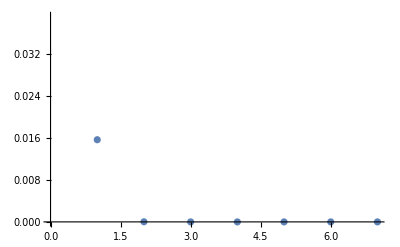

```mathematica
ListPlot[zZNlist]
```

```mathematica
(*airy:*)
aABJM[kk_]:=If[EvenQ[kk],
-Zeta[3]/(π^2*kk)-2/kk*Sum[m*(kk/2-m)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk/2-1}],
-Zeta[3]/(8*π^2*kk)+kk/4*Log[2]-1/kk*Sum[(kk+(-1)^m*(2*m-kk))/4*(kk-(kk+(-1)^m*(2*m-kk))/4)*Log[2*Sin[(2*π*m)/kk]],{m,1,kk-1}]
];
aA=1/2*(aABJM[6*k]+9*aABJM[2*k]);
cC=1/(3*π^2*k);
bB=(π^2*cC)/3-5/(18*k)+k/4;
(*
bB=(π^2*cC)/3-1/(3*k)+k/4;
*)
logZpert=Table[{nN,Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)]},{nN,0,8,0.01}];
```

```mathematica
range={{0,8},All};
imsize=400;
plot1=ListLogPlot[{zZNlist,logZpert,zZNlist},Joined->{False,True,False},PlotStyle->{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[1]]},PlotMarkers->{{"●",10},"",{"●",10}},PlotRange->range,Frame->True,FrameLabel->{"N","Z_(1, 0)(N)"},PlotLegends->Placed[{"Z_(1, 0)(N)","e^AC^(-1/3)Ai[C^(-1/3)(N-B)]"},{0.75,0.8}],ImageSize->imsize]
```

-Graphics-

```mathematica
deviations=Table[{√nN,Abs[zZN[[nN+1]]/(Exp[aA]*cC^(-1/3)*AiryAi[cC^(-1/3)*(nN-bB)])-1]},{nN,0,7}];
```

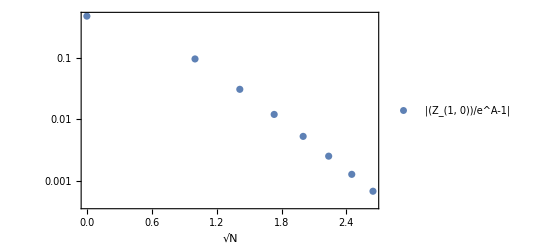

```mathematica
range=All;
origin=Automatic;
(*
range={{0,8},All};
*)
imsize=400;
(*
origin={0,0};
*)
plot2=ListLogPlot[deviations,AxesOrigin->origin,Frame->True,FrameLabel->{"√N",""},ImageSize->imsize,PlotLegends->Placed[{"|(Z_(1, 0))/e^A-1|"},{0.75,0.8}]]
```

```mathematica
Row[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Export["210122_affineD3_Z_vs_Airy_k1_M0.pdf",Style[%,LineBreakWithin->False]];
```